## MODELAGEM DA DINÂMICA PLANA DE AERONAVE SUPERSÔNICA DE PASSAGEIROS DURANTE FASE DE FREE-ROLL DA ATERRISSAGEM

## PME3380 - Modelagem de Sistemas Dinâmicos Prof. Dr. Agenor de Toledo Fleury Prof. Dr. Renato Maia Matarazzo Orsino

## Grupo K Lucas Retore Carboni - 12676091 Roberto Tetsuo Hamaoka - 10334770 Vitor Lucas Buter - 12555700

## Modelo principal - toque e free-roll

O equacionamento é baseado no seguinte modelo físico:
-Graphics-

e  são definidos como variáveis incrementais a partir da posição de equilíbrio dinâmico do avião transladando em pista plana com velocidade constante (M.R.U)
Importando as funções necessárias ao código

```mathematica
SetDirectory @ NotebookDirectory[];
<<Linearize.m
```

As coordenadas generalizadas são definidas como:

```mathematica
𝕢[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t]};
𝕧[t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]}; 
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = { Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, 𝕧[t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
α = 𝕢[t][[3]] + Subscript[Φ, 0];
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, PO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor P-O*)
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, GO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor G-O*)
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
D[Subscript[H, o], t] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]]
Subscript[TMB, m] = m*(D[𝕧[t][[1]], t]) + Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(𝕢[t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) - Subscript[L, ext][[2]]//FullSimplify;
```

{-Cos[Φ_0+θ[t]] D_GO θ'[t]^2-Sin[Φ_0+θ[t]] D_GO θ''[t],-Sin[Φ_0+θ[t]] D_GO θ'[t]^2+Cos[Φ_0+θ[t]] D_GO θ''[t]+q_2''[t],0}

### O espaço de estados

```mathematica
DIN = {Subscript[TMB, m], Subscript[TMB, M], TQMA};

Sol[t_] = Flatten @ Solve[
	(# == 0)& /@ DIN,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;

𝕩[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
F = (𝕩'[t] /.Sol[t]); 
F //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
-(M Cos[Φ_0+θ[t]] D_GO^2 (2 g M Cos[Φ_0+θ[t]]+Sin[Φ_0+θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol)+1/2 M D_GO (-S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2+4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2)+J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(2 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(Sec[Φ_0+θ[t]] (-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D Tan[Φ_0+θ[t]])+2 M Sin[Φ_0+θ[t]] D_GO^2 θ'[t]^2+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])+2 (g M-g M μ_rol Tan[Φ_0+θ[t]]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t])))))/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz))

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
Subscript[q, 1eq] = (Subscript[L, ext][[2]])/Subscript[k, r];
Subscript[q, 2eq] = (Subscript[L, ext][[2]])/Subscript[k, t] + (Subscript[L, ext][[2]])/Subscript[k, r];
```

```mathematica
POSequi = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINlin = Linearize[DIN, POSequi]; (*ELS -> Equação dinâmica não-linear*)

Sollin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINlin,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
	
Subscript[𝕩, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[F, lin] = (Subscript[𝕩, lin]'[t] /.Sollin[t]);
Subscript[F, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(2 M Cos[Φ_0] D_GO^2 ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+2 M S ρ Cos[Φ_0] D_GO D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))-2 J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(4 M (M Cos[Φ_0]^2 D_GO^2-J_oz))
(-S ρ D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))+D_GO (-2 g M Sin[Φ_0] (μ_rol+θ[t])+S ρ C_L (u_longit+u_vento)^2 (Cos[Φ_0]+μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t]))+2 Cos[Φ_0] (g M-g M μ_rol θ[t]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t]))))/(2 M Cos[Φ_0]^2 D_GO^2-2 J_oz))

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> ((25.66/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
𝔸 = CoefficientArrays[Subscript[F, lin], Subscript[𝕩, lin][t]][[2]]//Normal; 
𝔸 //FullSimplify//MatrixForm;

𝔹 = CoefficientArrays[Subscript[F, lin], 𝕦[t]][[2]]//Normal; 
𝔹 //MatrixForm;

ℂ = { {0,1,0,0,0,0}, {0,0,1,0,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}};
ℂ //MatrixForm;

𝔻 = {{0,0},{0,0},{0,0},{0,0}};
𝔻 //MatrixForm;

𝕩[t] //MatrixForm ;
𝕩'[t] //MatrixForm;
𝕦[t] //MatrixForm;
𝕪[t] //MatrixForm ;
𝔸.𝕩[t] //MatrixForm;

Polos = 𝔸/.(rep)/.(Subscript[Φ, 0]->a)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1)/.(Subscript[u, longit]->u);
Polos //MatrixForm
Eigenvalues[Polos]/.(v->-80);
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-125434/15 | 57434/15 | 0 | -13987/375 | 25549/750 | 0
-(2.20134×10^9)/(-1.68644×10^7+425920. Cos[a]^2) | (2.20134×10^9)/(-1.68644×10^7+425920. Cos[a]^2) | (688.225 (0.15714+0.01111 a+0.00017 a^2) u^2 Cos[a]^2)/(-1.68644×10^7+425920. Cos[a]^2)+(2.42 (0.0041+0.000041 u) (1.72656×10^6-125.132 (0.21999+0.07378 a-0.00165 a^2) u^2) Cos[a]^2)/(-1.68644×10^7+425920. Cos[a]^2)+(4.17828×10^6 Cos[a] Sin[a])/(-1.68644×10^7+425920. Cos[a]^2)-(688.225 (0.21999+0.07378 a-0.00165 a^2) u^2 Cos[a] Sin[a])/(-1.68644×10^7+425920. Cos[a]^2) | (1.9585×10^7)/(1.68644×10^7-425920. Cos[a]^2) | (1.72348×10^12)/(-1.48407×10^12+3.7481×10^10 Cos[a]^2) | 0
(5.05419×10^7 Sec[a])/(851840.-3.37288×10^7 Sec[a]^2) | -(5.05419×10^7 Sec[a])/(851840.-3.37288×10^7 Sec[a]^2) | -(3.79843×10^6 (0.0041+0.000041 u) Sec[a])/(851840.-3.37288×10^7 Sec[a]^2)-(625.659 (0.15714+0.01111 a+0.00017 a^2) u^2 Sec[a])/(851840.-3.37288×10^7 Sec[a]^2)+(275.29 (0.21999+0.07378 a-0.00165 a^2) (0.0041+0.000041 u) u^2 Sec[a])/(851840.-3.37288×10^7 Sec[a]^2)-(3.79843×10^6 Sec[a] Tan[a])/(851840.-3.37288×10^7 Sec[a]^2)+(625.659 (0.21999+0.07378 a-0.00165 a^2) u^2 Sec[a] Tan[a])/(851840.-3.37288×10^7 Sec[a]^2) | (224831. Sec[a])/(425920.-1.68644×10^7 Sec[a]^2) | (224831. Sec[a])/(-425920.+1.68644×10^7 Sec[a]^2) | 0)

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> ((25.66/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->11*Pi/180)/.(Subscript[u, longit]->280/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹/.(rep)/.(Subscript[Φ, 0]->11*Pi/180)/.(Subscript[u, longit]->280/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻}]
```

000100000000100000000100-125434/1557434/150-13987/37525549/750013600/397/30133.788-133.788-0.07690411.19029-1.19029000-1.507641.507640.0356107-0.01341320.013413200001000000001000000000100000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2461FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TF = TransferFunctionModel[SS, s]
```

(606504.+5395.96 s)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)(432.58+3.84859 s)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)-(60.8064 (-2.39316×10^-13-2.33707×10^-15 s+112.4 s^2+s^3))/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)-(0.0433693 (-1.31068×10^-12 s+112.4 s^2+s^3))/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)(606504. s+5395.96 s^2)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)(432.58 s+3.84859 s^2)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)(-6834.62 s^3-60.8064 s^4)/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)(-4.87469 s^3-0.0433693 s^4)/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.15067862432.5801662929589-60.80639254364632-0.04336926526957541606504.15067862432.5801662928398-6834.620433973583-4.874692515408241606496.9037255754606496.9037255753-21072.41907737784-21072.41907737784606496.9072442674606496.9072442674-21072.41907737784-21072.419077377841FalseFalseFalseAutomaticNoneAutomatic

```mathematica
(606504.15067862+5395.958681508539 s)/(606496.9037255754+5828.50652396288 s+8499.902068518812 s^2+38.48895166994061 s^3+s^4)(432.5801662929589+3.8485881772530774 s)/(606496.9037255753+5828.50652396288 s+8499.902068518812 s^2+38.48895166994061 s^3+s^4)-(60.80639254364632 (-2.393155492314662*^-13-2.3370659104635377*^-15 s+112.39970253239049 s^2+s^3))/(-21072.41907737784-202.50712723436797 s+606201.5825733319 s^2+5827.1692613139485 s^3+8499.867324453544 s^4+38.48895166994061 s^5+s^6)-(0.04336926526957541 (-1.3106843869150132*^-12 s+112.39970253519151 s^2+s^3))/(-21072.41907737784-202.50712723436797 s+606201.5825733319 s^2+5827.1692613139485 s^3+8499.867324453544 s^4+38.48895166994061 s^5+s^6)(606504.15067862 s+5395.958681508537 s^2)/(606496.9072442674+5828.5065398960305 s+8499.902068932779 s^2+38.48895166994061 s^3+s^4)(432.5801662928398 s+3.848588177252168 s^2)/(606496.9072442674+5828.5065398960305 s+8499.902068932779 s^2+38.48895166994061 s^3+s^4)(-6834.620433973583 s^3-60.806392543647235 s^4)/(-21072.41907737784-202.50712723436797 s+606201.5825733319 s^2+5827.1692613139485 s^3+8499.867324453544 s^4+38.48895166994061 s^5+s^6)(-4.874692515408241 s^3-0.04336926526957541 s^4)/(-21072.41907737784-202.50712723436797 s+606201.5825733319 s^2+5827.1692613139485 s^3+8499.867324453544 s^4+38.48895166994061 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.15067862432.5801662929589-60.80639254364632-0.04336926526957541606504.15067862432.5801662928398-6834.620433973583-4.874692515408241606496.9037255754606496.9037255753-21072.41907737784-21072.41907737784606496.9072442674606496.9072442674-21072.41907737784-21072.419077377841FalseFalseFalseAutomaticNoneAutomatic
```

(606504.+5395.96 s)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)(432.58+3.84859 s)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)-(60.8064 (-2.39316×10^-13-2.33707×10^-15 s+112.4 s^2+s^3))/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)-(0.0433693 (-1.31068×10^-12 s+112.4 s^2+s^3))/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)(606504. s+5395.96 s^2)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)(432.58 s+3.84859 s^2)/(606497.+5828.51 s+8499.9 s^2+38.489 s^3+s^4)(-6834.62 s^3-60.8064 s^4)/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)(-4.87469 s^3-0.0433693 s^4)/(-21072.4-202.507 s+606202. s^2+5827.17 s^3+8499.87 s^4+38.489 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.15067862432.5801662929589-60.80639254364632-0.04336926526957541606504.15067862432.5801662928398-6834.620433973583-4.874692515408241606496.9037255754606496.9037255753-21072.41907737784-21072.41907737784606496.9072442674606496.9072442674-21072.41907737784-21072.419077377841FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TF] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TF] [[4]][[1]] //MatrixForm
```

(-19.0614-89.7247 ⅈ
-19.0614+89.7247 ⅈ
-0.183061-8.4882 ⅈ
-0.183061+8.4882 ⅈ)

(-19.0614-89.7247 ⅈ
-19.0614+89.7247 ⅈ
-0.186399
-0.183061-8.4882 ⅈ
-0.183061+8.4882 ⅈ
0.186399)

```mathematica
TransferFunctionZeros[TF]
```

{{{-112.4},{-112.4}},{{-112.4,-4.61427×10^-8,4.61427×10^-8},{-112.4,0,1.16609×10^-14}},{{-112.4,0},{-112.4,0}},{{-112.4,0,0,0},{-112.4,0,0,0}}}

### Decomposição em frações parciais

```mathematica
FP = Apart[TF[s]]; 
OutputResponse[{SS,{0,0,0,-3,-3,0}}, 0, t] [[2]][[2]]//ComplexExpand //MatrixForm;
Plot[%, {t, 0, 2}];
FP//MatrixForm
IL = InverseLaplaceTransform[FP,s, t] //ComplexExpand //MatrixForm
(*https://lpsa.swarthmore.edu/Transient/TransMethTF.html#:~:text=To%20find%20the%20complete%20response,the%20zero%20input%20differential%20equation.*)
```

((72.8105+0.31783 s)/(72.0831+0.366122 s+1. s^2)+(-84.8107-0.31783 s)/(8413.86+38.1228 s+1. s^2) | (0.051931+0.000226688 s)/(72.0831+0.366122 s+1. s^2)+(-0.06049-0.000226688 s)/(8413.86+38.1228 s+1. s^2)
-0.00104961/(-0.186399+1. s)+0.00104989/(0.186399+1. s)+(-0.820097-0.00358187 s)/(72.0831+0.366122 s+1. s^2)+(0.955718+0.00358159 s)/(8413.86+38.1228 s+1. s^2) | -(7.48622×10^-7)/(-0.186399+1. s)+(7.48821×10^-7)/(0.186399+1. s)+(-0.000584922-2.55471×10^-6 s)/(72.0831+0.366122 s+1. s^2)+(0.000681652+2.55452×10^-6 s)/(8413.86+38.1228 s+1. s^2)
(-22.9102+72.6941 s)/(72.0831+0.366122 s+1. s^2)+(2674.18-72.6941 s)/(8413.86+38.1228 s+1. s^2) | (-0.0163403+0.051848 s)/(72.0831+0.366122 s+1. s^2)+(1.90732-0.051848 s)/(8413.86+38.1228 s+1. s^2)
-0.000195647/(-0.186399+1. s)-0.000195699/(0.186399+1. s)+(0.258192-0.818786 s)/(72.0831+0.366122 s+1. s^2)+(-30.135+0.819177 s)/(8413.86+38.1228 s+1. s^2) | -(1.39542×10^-7)/(-0.186399+1. s)-(1.39579×10^-7)/(0.186399+1. s)+(0.000184152-0.000583987 s)/(72.0831+0.366122 s+1. s^2)+(-0.0214933+0.000584266 s)/(8413.86+38.1228 s+1. s^2))

(-0.158915 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+0.158915 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+0.158915 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-0.158915 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.438856 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.438856 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-4.2855 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+4.2855 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+4.2855 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-0.158915 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.438856 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+0.158915 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (-0.438856 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+4.2855 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-4.2855 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.438856 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-0.158915 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.158915 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+0.158915 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+0.158915 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+0.158915 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+4.2855 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.158915 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.438856 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]) | -0.000113344 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+0.000113344 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+0.000113344 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-0.000113344 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.000313008 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.000313008 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-0.00305657 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+0.00305657 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+0.00305657 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-0.000113344 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.000313008 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+0.000113344 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (-0.000313008 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+0.00305657 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-0.00305657 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.000313008 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-0.000113344 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.000113344 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+0.000113344 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+0.000113344 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+0.000113344 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+0.00305657 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.000113344 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.000313008 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t])
0.+0.00104989 ⅇ^(-0.186399 t)-0.00104961 ⅇ^(0.186399 t)+0.00179079 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-0.00179093 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-0.00179093 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.00179079 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-0.00494539 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+0.00494539 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+0.0482695 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-0.0482695 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-0.0482695 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+0.00179093 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+0.00494539 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.00179079 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (0.+0.00494539 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-0.0482695 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+0.0482695 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-0.00494539 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.00179079 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+0.00179079 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-0.00179093 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-0.00179093 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-0.00179093 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-0.0482695 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+0.00179079 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+0.00494539 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]) | 0.+7.48821×10^-7 ⅇ^(-0.186399 t)-7.48622×10^-7 ⅇ^(0.186399 t)+1.27726×10^-6 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-1.27736×10^-6 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-1.27736×10^-6 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+1.27726×10^-6 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-3.52723×10^-6 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+3.52723×10^-6 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+0.0000344275 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-0.0000344275 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-0.0000344275 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+1.27736×10^-6 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+3.52723×10^-6 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-1.27726×10^-6 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (0.+3.52723×10^-6 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-0.0000344275 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+0.0000344275 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-3.52723×10^-6 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+1.27726×10^-6 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+1.27726×10^-6 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-1.27736×10^-6 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-1.27736×10^-6 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-1.27736×10^-6 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-0.0000344275 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+1.27726×10^-6 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+3.52723×10^-6 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t])
-36.3471 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+36.3471 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+36.3471 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-36.3471 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-22.6238 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+22.6238 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+2.13341 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-2.13341 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-2.13341 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-36.3471 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+22.6238 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+36.3471 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (22.6238 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-2.13341 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+2.13341 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-22.6238 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-36.3471 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-36.3471 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+36.3471 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+36.3471 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+36.3471 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-2.13341 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-36.3471 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+22.6238 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]) | -0.025924 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+0.025924 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+0.025924 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-0.025924 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-0.0161361 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+0.0161361 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+0.00152162 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-0.00152162 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-0.00152162 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-0.025924 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+0.0161361 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+0.025924 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (0.0161361 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-0.00152162 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]+0.00152162 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]-0.0161361 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]-0.025924 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.025924 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]+0.025924 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+0.025924 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+0.025924 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]-0.00152162 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.025924 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]+0.0161361 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t])
0.-0.000195699 ⅇ^(-0.186399 t)-0.000195647 ⅇ^(0.186399 t)+0.409589 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-0.409393 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-0.409393 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.409589 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.254945 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.254945 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-0.0240381 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+0.0240381 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+0.0240381 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+0.409393 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.254945 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.409589 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (0.-0.254945 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+0.0240381 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-0.0240381 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.254945 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.409589 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+0.409589 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-0.409393 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-0.409393 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-0.409393 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+0.0240381 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+0.409589 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.254945 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]) | 0.-1.39579×10^-7 ⅇ^(-0.186399 t)-1.39542×10^-7 ⅇ^(0.186399 t)+0.000292133 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]-0.000291994 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-0.000291994 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.000292133 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.000181836 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]-0.000181836 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-0.0000171448 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]+0.0000171448 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]+0.0000171448 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+0.000291994 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]-0.000181836 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.000292133 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]+ⅈ (0.-0.000181836 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t]+0.0000171448 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t]-0.0000171448 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Cos[0.+16.9764 t]+0.000181836 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Cos[0.+179.449 t]+0.000292133 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t]+0.000292133 ⅇ^(0.-19.0614 t) Cos[0.+179.449 t] Sin[0.-89.7247 t]-0.000291994 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t]-0.000291994 ⅇ^(0.-0.183061 t) Cos[0.+16.9764 t] Sin[0.-8.4882 t]-0.000291994 ⅇ^(0.-0.183061 t) Cos[0.-8.4882 t] Sin[0.+16.9764 t]+0.0000171448 ⅇ^(0.-0.183061 t) Sin[0.-8.4882 t] Sin[0.+16.9764 t]+0.000292133 ⅇ^(0.-19.0614 t) Cos[0.-89.7247 t] Sin[0.+179.449 t]-0.000181836 ⅇ^(0.-19.0614 t) Sin[0.-89.7247 t] Sin[0.+179.449 t]))

### Diagrama de Bode

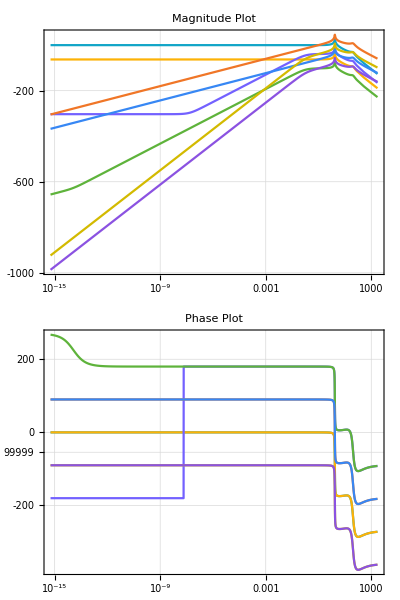

```mathematica
BodePlot[TF, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Pós toque

### Modelo incluindo trem de pouso frontal

-Graphics-

```mathematica
Subscript[𝕢, T][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t]};
Subscript[𝕧, T][t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = {Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, Subscript[𝕧, T][t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, PO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor P-O*);
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, GO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
Subscript[ρ, FO] = {Subscript[D, FO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, FO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[F, f] = {0, -Subscript[k, Tf]*(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]), t]), 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, Tf] = Cross[Subscript[ρ, FO], Subscript[F, f]] //FullSimplify;
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso] - Subscript[M, Tf])[[3]]//FullSimplify
```

-1/2 S ρ (Sin[Φ_0+θ[t]] C_D+Cos[Φ_0+θ[t]] C_L) D_PO (u_longit+u_vento)^2+Cos[Φ_0+θ[t]] D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t]))+J_oz θ''[t]+1/2 D_GO (Sin[Φ_0+θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol+2 M Cos[Φ_0+θ[t]] (g+q_2''[t]))

### Aplicação do TMB no conjunto do trem de pouso (m e mf) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[Subscript[𝕧, T][t][[1]], t]) + Subscript[k, r]*(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]) - Subscript[c, t]*(D[(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]), t]) //FullSimplify;
Subscript[TMB, mf] = Subscript[m, f]*(D[Subscript[𝕧, T][t][[4]], t]) + Subscript[k, rf]*(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]) + Subscript[c, rf]*(D[(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]), t]) - Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) + Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) - Subscript[L, ext][[2]] //FullSimplify
noequi =  Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) //FullSimplify
```

-1/2 S ρ C_L (u_longit+u_vento)^2+k_t (-q_1[t]+q_2[t])+k_Tf (Sin[Φ_0+θ[t]] D_FO+q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (Cos[Φ_0+θ[t]] D_FO θ'[t]+q_2'[t]-q_3'[t])+M (D_GO (-Sin[Φ_0+θ[t]] θ'[t]^2+Cos[Φ_0+θ[t]] θ''[t])+q_2''[t])

k_t (-q_1[t]+q_2[t])+k_Tf (Sin[Φ_0+θ[t]] D_FO+q_2[t]-q_3[t])

### O espaço de estados

```mathematica
DINf = {Subscript[TMB, m], Subscript[TMB, M], TQMA, Subscript[TMB, mf]};

Solf[t_] = Flatten @ Solve[
	(# == 0)& /@ DINf,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
𝕩f[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Ff = (𝕩f'[t] /.Solf[t]); 
Ff //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-4 g M Cos[Φ_0+θ[t]]^2+Sin[2 (Φ_0+θ[t])] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+M D_GO (S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2-4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2-4 Cos[Φ_0+θ[t]]^2 D_FO^2 (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+4 Cos[Φ_0+θ[t]]^2 D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t])))+2 J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])-2 (k_t (q_1[t]-q_2[t])+k_Tf (-q_2[t]+q_3[t])+c_t (q_1'[t]-q_2'[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(4 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(-S ρ Sec[Φ_0+θ[t]] C_L D_PO (u_longit+u_vento)^2+2 D_FO^2 k_Tf Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit^2 Tan[Φ_0+θ[t]]-2 S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit u_vento Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_vento^2 Tan[Φ_0+θ[t]]+2 Sec[Φ_0+θ[t]] D_FO k_Tf q_2[t]-2 Sec[Φ_0+θ[t]] D_FO k_Tf q_3[t]+2 c_Tf D_FO^2 θ'[t]+2 M D_GO^2 Tan[Φ_0+θ[t]] θ'[t]^2+2 Sec[Φ_0+θ[t]] c_Tf D_FO q_2'[t]+D_GO (S ρ Sec[Φ_0+θ[t]] C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])-2 (D_FO (k_Tf Tan[Φ_0+θ[t]]+c_Tf θ'[t])+Sec[Φ_0+θ[t]] (-g M+g M μ_rol Tan[Φ_0+θ[t]]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))-2 Sec[Φ_0+θ[t]] c_Tf D_FO q_3'[t])/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
eqi = {{-Subscript[k, t], Subscript[k, t]+Subscript[k, Tf], -Subscript[k, Tf]},{-Subscript[k, t]-Subscript[k, r], Subscript[k, t], 0}, {0, Subscript[k, Tf], -Subscript[k, Tf]-Subscript[k, rf]}};
vari = {Subscript[q, 1e], Subscript[q, 2e], Subscript[q, 3e]};
for = {-M*g, m*g, Subscript[m, f]*g};
solucao = LinearSolve[eqi, for];
rep = {Subscript[k, t] -> 11486800, Subscript[c, t] -> 1021960, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, Subscript[k, Tf] -> 5743400, Subscript[c, Tf] -> 51098, Subscript[k, rf]-> 3400000, Subscript[c, rf] -> 2*2425, m -> 3000, Subscript[m, f] -> 1000, M -> 88000, g->9.81};
solucao/.rep
```

{-0.0495143,-0.105576,-0.0673899}

```mathematica
POSequif = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0, Subscript[q, 3][t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINflin = Linearize[DINf, POSequif]; (*ELS -> Equação dinâmica não-linear*)

Solflin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINflin,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
Subscript[𝕩f, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Subscript[Ff, lin] = (Subscript[𝕩f, lin]'[t] /.Solflin[t]);
Subscript[Ff, lin] //TrigReduce //FullSimplify //MatrixForm 
(*aquiiiiiiiiiiiiiiiiiiiiiiiii*)
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M Cos[Φ_0] D_GO^2 ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+M Cos[Φ_0] D_GO (S ρ D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))-D_FO^2 (k_Tf (Sin[2 Φ_0]+2 Cos[2 Φ_0] θ[t])+2 Cos[Φ_0]^2 c_Tf θ'[t])+2 Cos[Φ_0] D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t])))+J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (k_Tf (Sin[Φ_0]+Cos[Φ_0] θ[t])+Cos[Φ_0] c_Tf θ'[t])-2 (k_t (q_1[t]-q_2[t])+k_Tf (-q_2[t]+q_3[t])+c_t (q_1'[t]-q_2'[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(2 M (M Cos[Φ_0]^2 D_GO^2-J_oz))
(D_GO (S ρ Sec[Φ_0] C_L (u_longit+u_vento)^2 (1+μ_rol (Tan[Φ_0]+θ[t]))-2 (D_FO (k_Tf (Tan[Φ_0]+θ[t])+c_Tf θ'[t])+Sec[Φ_0] (-g M+g M (Tan[Φ_0] θ[t]+μ_rol (Tan[Φ_0]+θ[t]))+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))+Sec[Φ_0] (S ρ D_PO (u_longit+u_vento)^2 (-C_D (Tan[Φ_0]+θ[t])+C_L (-1+Tan[Φ_0] θ[t]))+2 D_FO^2 (k_Tf (Sin[Φ_0]+Cos[2 Φ_0] Sec[Φ_0] θ[t])+Cos[Φ_0] c_Tf θ'[t])+2 D_FO (k_Tf (q_2[t]-q_3[t])+c_Tf (q_2'[t]-q_3'[t]))))/(2 M D_GO^2-2 Sec[Φ_0]^2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (k_Tf (Sin[Φ_0]+Cos[Φ_0] θ[t])+Cos[Φ_0] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

```mathematica
𝔸f = CoefficientArrays[Subscript[Ff, lin], Subscript[𝕩f, lin][t]][[2]]//Normal; 
𝔸f //FullSimplify//MatrixForm;

𝔹f = CoefficientArrays[Subscript[Ff, lin], 𝕦[t]][[2]]//Normal; 
𝔹f //MatrixForm;

ℂf = { {0,1,0,0,0,0,0,0}, {0,0,1,0,0,0,0,0}, {0,0,0,0,0,1,0,0}, {0,0,0,0,0,0,1,0}};
ℂf //MatrixForm;

𝔻f = {{0,0},{0,0},{0,0},{0,0}};
𝔻f //MatrixForm;
 
𝕩f[t] //MatrixForm ;
𝕩f'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.15714, Subscript[C, L] -> 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, Subscript[k, Tf] -> 5743400, Subscript[c, Tf] -> 51098, Subscript[k, rf]-> 3400000, Subscript[c, rf] -> 2425, m -> 3000, Subscript[m, f] -> 1500, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, Subscript[D, FO] -> 32.5, ρ -> 1.2923, S -> ((25.6/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂf, 𝔻f}]
```

0000100000000001000000000010000000000100-125434/1557434/1500-13987/37525549/7500013600/397/30133.739-176.921-1407.5143.18211.18985-1.57403-12.16630.38418300-1.49598-8.8059-307.56810.3019-0.0133095-0.0783445-2.902490.09165400057434/15121254.-30478/5025549/7501078.78-17841/5006800/397/600100000000001000000000000100000000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TFf = TransferFunctionModel[SS, s]
```

(6264.8 (6.0482×10^7+1.1787×10^6 s+757580. s^2+11019.3 s^3+150.923 s^4+s^5))/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(4.46828 (6.0482×10^7+1.1787×10^6 s+757580. s^2+11019.3 s^3+150.923 s^4+s^5))/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(0.000244141+0.0000114441 s+1.50658×10^8 s^2+1.94026×10^6 s^3+21906.2 s^4+147.413 s^5)/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(0.0000610352+0.0000104904 s+107455. s^2+1383.86 s^3+15.6243 s^4+0.10514 s^5)/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(3.78908×10^11 s+7.38432×10^9 s^2+4.74609×10^9 s^3+6.90338×10^7 s^4+945500. s^5+6264.8 s^6)/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(2.7025×10^8 s+5.26676×10^6 s^2+3.38508×10^6 s^3+49237.3 s^4+674.364 s^5+4.46828 s^6)/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(-3.8147×10^-6 s+1.90735×10^-6 s^2+1.50658×10^8 s^3+1.94026×10^6 s^4+21906.2 s^5+147.413 s^6)/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)(-9.53674×10^-7 s+107455. s^3+1383.86 s^4+15.6243 s^5+0.10514 s^6)/(3.78908×10^11+7.65457×10^9 s+1.00618×10^10 s^2+1.51171×10^8 s^3+5.66715×10^7 s^4+592672. s^5+16451.1 s^6+77.4572 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s246264.7986707045934.4682755224639560.0002441406250.000061035156253.7890775746432837e112.702503858385296e8-3.814697265625e-6-9.5367431640625e-73.7890775746432776e113.7890775746432776e113.7890775746432776e113.7890775746432776e113.7890775746432776e113.7890775746432776e113.7890775746432776e113.7890775746432776e111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TFf] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TFf] [[4]][[1]] //MatrixForm
```

(-19.2462-77.1305 ⅈ
-19.2462+77.1305 ⅈ
-19.0661-89.7223 ⅈ
-19.0661+89.7223 ⅈ
-0.267019-11.5004 ⅈ
-0.267019+11.5004 ⅈ
-0.149247-7.33694 ⅈ
-0.149247+7.33694 ⅈ)

(-19.2462-77.1305 ⅈ
-19.2462+77.1305 ⅈ
-19.0661-89.7223 ⅈ
-19.0661+89.7223 ⅈ
-0.267019-11.5004 ⅈ
-0.267019+11.5004 ⅈ
-0.149247-7.33694 ⅈ
-0.149247+7.33694 ⅈ)

```mathematica
TransferFunctionZeros[TFf]
```

{{{-112.4,-19.0653-78.9258 ⅈ,-19.0653+78.9258 ⅈ,-0.19621-9.03222 ⅈ,-0.19621+9.03222 ⅈ},{-112.4,-19.0653-78.9258 ⅈ,-19.0653+78.9258 ⅈ,-0.19621-9.03222 ⅈ,-0.19621+9.03222 ⅈ}},{{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-2.75455×10^-14-1.27299×10^-6 ⅈ,-2.75455×10^-14+1.27299×10^-6 ⅈ},{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-4.51556×10^-11-0.0000238329 ⅈ,-4.51556×10^-11+0.0000238329 ⅈ}},{{-112.4,-19.0653-78.9258 ⅈ,-19.0653+78.9258 ⅈ,-0.19621-9.03222 ⅈ,-0.19621+9.03222 ⅈ,0},{-112.4,-19.0653-78.9258 ⅈ,-19.0653+78.9258 ⅈ,-0.19621-9.03222 ⅈ,-0.19621+9.03222 ⅈ,0}},{{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-1.59123×10^-7,0,1.59123×10^-7},{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-2.97911×10^-6,0.,2.97911×10^-6}}}

### Diagrama de Bode

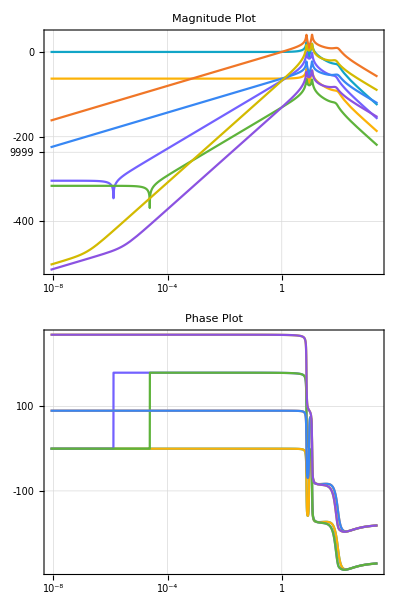

```mathematica
BodePlot[TFf, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Exportando o aquivo .m do espaço de estados

Para exportar outro espaço de estados, basta substituir o argumento da 4 linha da terceira célula de código por:
WriteString[fileD, (#/.(({ii_}→vv_):>(StringReplace[StringReplace[ToString @ StringForm[“    ``;”, (vv /. crule //CForm)], csqrule], csorule]<>”\n”)))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩’[t]/.NOMEDASOLUCAO[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};
```

```mathematica
fileD = OpenWrite["trab_esp_linearizado0.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(Subscript[𝕩f, lin]'[t]/.Solflin[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```